```mathematica
Expand[ ((a+1)(a+2)-6(a+1)+6)/2]
```

1-(3 a)/2+a^2/2

```mathematica
Expand[ (a+1)(a+2)(a+3)/6 - 2(a+1)(a+2) +6(a+1)-4]
```

-1+(11 a)/6-a^2+a^3/6

```mathematica
SS[k_] := Product[ a+j, {j,1,k-1}]/((k-1)!)
```

```mathematica
SS[6]
```

1/120 (1+a) (2+a) (3+a) (4+a) (5+a)

```mathematica
SSS[k_] := Sum[(-1)^(k-j) Binomial[ k, j ] SS[j], {j,1,k}]
```

```mathematica
Expand[SSS[4]]
```

-1+(11 a)/6-a^2+a^3/6

```mathematica
Expand[(a-1)(a-2)(a-3)/6]
```

-1+(11 a)/6-a^2+a^3/6

```mathematica
KK[a_,k_] := -((-1)^k (-1-a+k)!)/((-a)! (-1+k)!)
```

```mathematica
JJ[a_,k_] := (a-1)!/( (k-1)!(a-k)! )
```

```mathematica
KK[3,3]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
JJ[9,3]
```

28

```mathematica
DD[n_,k_] := Sum[ DD[n/j, k-1], {j,2,n}]
```

```mathematica
DD[n_,0] := 1
```

```mathematica
DDD[n_, k_ ]:=DD[n,k]-DD[n-1,k]
```

```mathematica
DDD[2^8,3]
```

21

```mathematica
FullSimplify[JJ[a,k]]
```

Gamma[a]/(Gamma[1+a-k] Gamma[k])

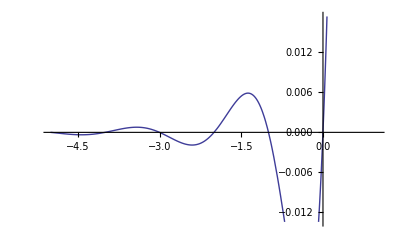

```mathematica
Plot[ Gamma[5]/(Gamma[1+5-k] Gamma[k]), {k,-5,1}]
```

```mathematica
FF[n_,k_]:=Product[Binomial[FactorInteger[n][[j]][[2]]+k-1,FactorInteger[n][[j]][[2]]],{j,1,Length[FactorInteger[n]]}]

FF2[n_,k_]:=FF[n,k]/k

FF3[n_,k_]:=Sum[FF2[j,k],{j,2,n}]



GG[n_,k_,a_]:=Sum[(k MangoldtLambda[j])/(a Log[j]) (1+GG[n/j,k,a+1]),{j,2,n}]
```

```mathematica
XX[n_,k_]:=Product[(FactorInteger[n][[j]][[2]]-1)!/((FactorInteger[n][[j]][[2]]-k)! (k-1)! ),{j,1,Length[FactorInteger[n]]}]
```

```mathematica
XX[2^2 * 3,3]
```

0

```mathematica
DDD[2^2 * 3,3]
```

3

```mathematica
(2+1)(2+2)(1+1)(1+2)/4 - 3(2+1)(1+1) + 3
```

3

```mathematica
Expand[(a+1)(b+1)-2]
```

-1+a+b+a b

```mathematica
Expand[(a+1)(a+2)(b+1)(b+2)/(2 2) - 3(a+1)(b+1) + 3]
```

1-(3 a)/2+a^2/2-(3 b)/2-(3 a b)/4+(3 a^2 b)/4+b^2/2+(3 a b^2)/4+(a^2 b^2)/4

```mathematica
Expand[(a-1)(a-2)(b+1)(b+2)/4]
```

1-(3 a)/2+a^2/2+(3 b)/2-(9 a b)/4+(3 a^2 b)/4+b^2/2-(3 a b^2)/4+(a^2 b^2)/4

```mathematica
Simplify[3 a+3 b+3 a b]
```

3 (a+b+a b)

```mathematica
Expand[(a-1)(a-2)(b-1)(b-2)/4]-Expand[(a+1)(a+2)(b+1)(b+2)/(2 2) - 3(a+1)(b+1) + 3]
```

3 a b-(3 a^2 b)/2-(3 a b^2)/2

```mathematica
Expand[(a+1)(a+2)(b+1)(b+2)/4]-Expand[(a+1)(a+2)(b+1)(b+2)/(2 2) - 3(a+1)(b+1) + 3]
```

3 a+3 b+3 a b

```mathematica
SR[k_] := Product[ a+j, {j,1,k-1}]/((k-1)!)Product[ b+j, {j,1,k-1}]/((k-1)!)
```

```mathematica
SR[4]
```

1/36 (1+a) (2+a) (3+a) (1+b) (2+b) (3+b)

```mathematica
(Pochhammer[1+a,-1+k] Pochhammer[1+b,-1+k])/((-1+k)!)^2
```

(Pochhammer[1+a,-1+k] Pochhammer[1+b,-1+k])/((-1+k)!)^2

```mathematica
SSR[k_] := Sum[(-1)^(k-j) Binomial[ k, j ] SR[j], {j,1,k}]
```

```mathematica
SSR[3]
```

3-3 (1+a) (1+b)+1/4 (1+a) (2+a) (1+b) (2+b)

```mathematica
SR2[k_, a_, b_] := Product[ a+j, {j,1,k-1}]/((k-1)!)Product[ b+j, {j,1,k-1}]/((k-1)!)
```

```mathematica
SSR2[k_,a_,b_] := Sum[(-1)^(j) Binomial[ k, k-j ] SR2[k-j,a,b], {j,0,4k}]
```

```mathematica
SSR2[5.1,a,b]
```

3.70237×10^15-9.86502 (1+a) (1+b)+2.1648 (1+a) (2+a) (1+b) (2+b)-0.109886 (1+a) (2+a) (3+a) (1+b) (2+b) (3+b)+0.00128175 (1+a) (2+a) (3+a) (4+a) (1+b) (2+b) (3+b) (4+b)

```mathematica
Plot[SSR2,
```

```mathematica
ST[k_] := Product[ a+j, {j,1,k-1}]/((k-1)!)Product[ b+j, {j,1,k-1}]/((k-1)!)Product[ c+j, {j,1,k-1}]/((k-1)!)
```

```mathematica
ST[k]
```

(Pochhammer[1+a,-1+k] Pochhammer[1+b,-1+k] Pochhammer[1+c,-1+k])/((-1+k)!)^3

```mathematica
SST[k_] := Sum[(-1)^(k-j) Binomial[ k, j ] ST[j], {j,1,k}]
```

```mathematica
FullSimplify[SST[k]]
```

-(-1)^k k HypergeometricPFQ[{1+a,1+b,1+c,1-k},{1,1,2},1]

```mathematica
SST[k]
```

-(-1)^k k HypergeometricPFQ[{1+a,1+b,1+c,1-k},{1,1,2},1]

```mathematica
-(-1)^k k HypergeometricPFQ[{1+a,1-k},{2},1]
```

-(-1)^k k HypergeometricPFQ[{1+a,1-k},{2},1]

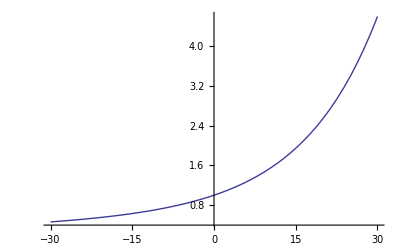

```mathematica
Plot[HypergeometricPFQ[{1,1},{3,3,3},x],{x,-30,30}]
```

```mathematica
-(-1)^3 3 HypergeometricPFQ[{1+a,1+b,1-3},{1,2},1]
```

```mathematica
Expand[3 (1-(1+a) (1+b)+1/12 (1+a) (2+a) (1+b) (2+b))]
```

1-(3 a)/2+a^2/2-(3 b)/2-(3 a b)/4+(3 a^2 b)/4+b^2/2+(3 a b^2)/4+(a^2 b^2)/4

```mathematica
SSR[3]
```

```mathematica
Expand[3-3 (1+a) (1+b)+1/4 (1+a) (2+a) (1+b) (2+b)]
```

1-(3 a)/2+a^2/2-(3 b)/2-(3 a b)/4+(3 a^2 b)/4+b^2/2+(3 a b^2)/4+(a^2 b^2)/4

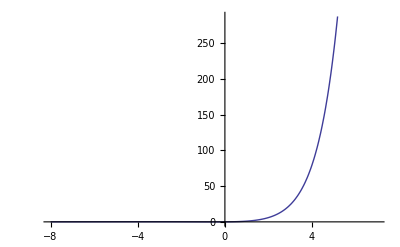

```mathematica
Plot[k HypergeometricPFQ[{1+1,1+1,1-k},{1,2},-1],{k,-8,7}]
```

```mathematica
AA[a_, b_, k_]:=-(-1)^k k HypergeometricPFQ[{1+a,1+b,1-k},{1,2},1]
```

```mathematica
AA[4,2,3]
```

48

```mathematica
BB[a_, b_, k_] :=k HypergeometricPFQ[{1+a,1+b,1-k},{1,2},1]
```

```mathematica
BB[4,2,2]
```

ComplexInfinity

```mathematica
DDD[2^7 3^3,3]
```

267

```mathematica
Plot[ AA[n,1,1.5], {n,-8,8}]
```

-Graphics-

```mathematica
Binomial[4,0]
```

1

```mathematica
Pochhammer[4,-1]
```

1/3

```mathematica
Binomial[4.5,-600.5]
```

```mathematica
8.530219409113667*^-15
```

```mathematica
Product[ j,{j,8,2}]
```

1

```mathematica
TT[a_, k_ ]:= Product[ a+j, {j,1,k}]
```

```mathematica
TT[1,-4]
```

1

```mathematica
TT2[ k_, j_, a_, b_] := (-1)^j Binomial[ k, k-j] TT[ a, k-j-1] TT[b,k-j-1]/(((k-j-1)!)^2)
```

```mathematica
TT2[4.5,0,a,b]
```

0.00739114 (1+a) (2+a) (3+a) (1+b) (2+b) (3+b)

```mathematica
TT3[ n_, a_, b_ ] := Sum[ TT2[n,j,a,b], {j,0, 30}]
```

```mathematica
TT2[4.2,15,a,b]
```

-2.23076×10^8

```mathematica
DDD[2^3 3^2, 4]
```

28

```mathematica
Plot[ TT3[n,3,2],{n,4,5}]
```

-Graphics-

```mathematica
TT3[4.1,3,2]
```

-9.51784×10^43

```mathematica
Binomial[4.1, 4.1-15]
```

6.02929×10^-6

```mathematica
(-1)^15 Binomial[ 4.1, 4.1-15] TT[ a, 4.1-15-1] TT[b,4.1-15-1]/(((4.1-15-1)!)^2)
```

-5.70761×10^7

```mathematica
(((4.1-15-1)!)^2)
```

1.05636×10^-13

```mathematica
Gamma[4.1-15]
```

-3.25017×10^-7

```mathematica
TT[ a, 4.1-15-1]
```

1

```mathematica
SS[n_, k_,a_] := Sum[ a(1/k-SS[n/j,k+1,a]),{j,2,n}]
```

```mathematica
N[SS[100,1,2]]
```

11.7333

```mathematica
RP[n_]:=N[MangoldtLambda[n]/Log[n]]
RR[ n_ ]:= Sum[ RP[j],{j,2,n}]
```

```mathematica
RR[1000]
```

176.696

```mathematica
RP2[n_] := Sum[ RP[j] RR[n/j],{j,2,n}]
```

```mathematica
RP[1]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
N[SS[100,1,2]]
```

11.7333

```mathematica
RR[100]
```

28.5333

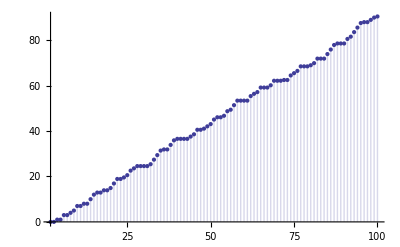

```mathematica
DiscretePlot[RP2[n],{n,2,100}]
```

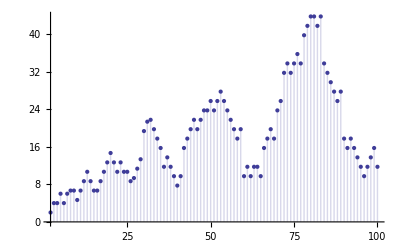

```mathematica
DiscretePlot[SS[n,1,2],{n,2,100}]
```

```mathematica
XX[n_,k_,a_] := Sum[ a RP[j](1/(k!) + XX[n/j, k+1,a]),{j,2,n}]
```

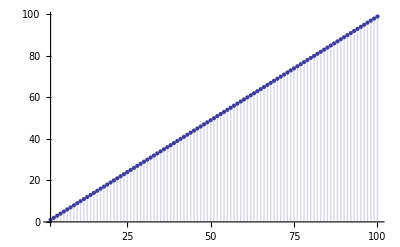

```mathematica
DiscretePlot[XX[n,1,1],{n,2,100}]
```

```mathematica
Log[1.1]
```

0.0953102

```mathematica
FF[n_,k_]:=Product[Binomial[FactorInteger[n][[j]][[2]]+k-1,FactorInteger[n][[j]][[2]]],{j,1,Length[FactorInteger[n]]}]
FF[1,k_] := 1
FF2[n_,k_]:=FF[n,k]/k

FF3[n_,k_]:=Sum[FF2[j,k],{j,2,n}]

GG[n_,k_,a_]:=Sum[(k MangoldtLambda[j])/(a Log[j]) (1+GG[n/j,k,a+1]),{j,2,n}]
```

```mathematica
FF2[1,.000001]
```

1.×10^6

```mathematica
FFX[ k_] := FF2[1,k] Log[1+k]
```